```mathematica
Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[n,{n,1,20}]
```

```mathematica
f[x_]:=x^2;
```

```mathematica
#^2 &;
```

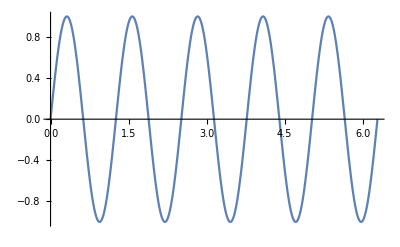

```mathematica
n=5;
Plot[Sin[n x],{x,0,2Pi}]
```

```mathematica
Manipulate[
Plot[Sin[n x],{x,0,2Pi}],
{n,1,20}
]
```

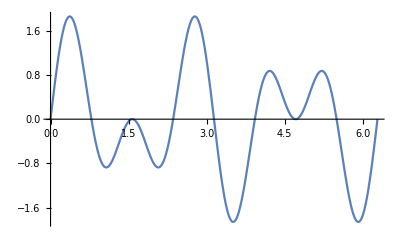

```mathematica
n1=5;
n2=3;
Plot[Sin[n1 x]+Sin[n2 x],{x,0,2Pi}]
```

```mathematica
Manipulate[
Plot[Sin[n1 x]+Sin[n2 x],{x,0,2Pi}],
{n1, 1, 5},
{n2,10,20}
]
```

```mathematica
(* Če hočem več stvari v graphics povedat, moram podat seznam {pt,{-1,-1},{1,1}}.
PlotRange mormo dat -> 1 da dela.*)

pt={0,0};
Manipulate[
Graphics[{
PointSize[0.1],
Point[pt]
},PlotRange->1],
{pt,{-1,-1},{1,1}} 
]
```

```mathematica
(*Želvja grafika; povem spodnjo levo in zgornjo desno točko, potem naredi sam pravokotnik *)
```